## Project individual tensors

The following function develos the projector for tensors of a particular degree

```mathematica
ProjectTensor[degree_,nx_,ny_]:=Module[{result},
Which[degree == 0,
result = 1,
degree == 1,
result = {nx,ny,-ny,nx};
result=ArrayReshape[result,{2,2}];,
degree == 2,
result = {nx*nx,2*nx*ny,ny*ny,-nx*ny,nx*nx-ny*ny,nx*ny,ny*ny,-2*nx*ny,nx*nx};
result=ArrayReshape[result,{3,3}];,
degree == 3,
result = {nx*nx*nx,3*ny*nx*nx,3*nx*ny*ny,ny*ny*ny,-ny*nx*nx,nx*nx*nx-2*nx*ny*ny,2*ny*nx*nx-ny*ny*ny,nx*ny*ny,nx*ny*ny,-2*ny*nx*nx+ny*ny*ny,nx*nx*nx-2*nx*ny*ny,ny*nx*nx,-ny*ny*ny,3*nx*ny*ny,-3*ny*nx*nx,nx*nx*nx};
result=ArrayReshape[result,{4,4}];
];


result
]
```

## system A

```mathematica
θExactSystemA[θwplus1_,θwminus1_,τ_]:= Block[{deltaθ,θbar,f,y},

deltaθ = θwplus1-θwminus1;
θbar = (θwplus1+θwminus1)/2;

f[y_]:=(deltaθ y)/(2(1+τ))+θbar ;

f[y]

]
```

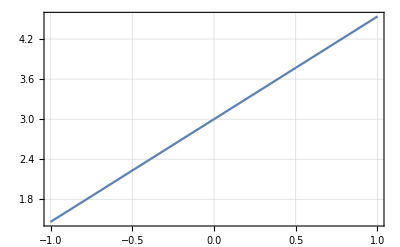

```mathematica
Plot[θExactSystemA[5,1,0.3],{y,-1,1},GridLines->Automatic,Frame->True]
```

```mathematica
trialexactθ[5,1,0.3]/.{y->-1}
```

1.46154

# R13

```mathematica
neqnR13 = 17;
nbc13 = 6;
(*variables that are used to derive the system. Ref. Manuel's paper*)
WR13 =  {w0,wn,wt,w1,wnn,wnt,wtt,w1n,w1t,wnnn,wnnt,wntt,wttt,w2,w1nn,w1nt,w1tt};

WR13globalcord =  {w0,wx,wy,w1,wxx,wxy,wyy,w1x,w1y,wxxx,wxxy,wxyy,wyyy,w2,w1xx,w1xy,w1yy};

(*transformation of w to usual variables in local coordinates*)
UR13 = {w0->ρ,wn->vn,wt->vt,w1->-3/2 θ,wnn->σnn,wnt->σnt,wtt->σtt,w1n->-qn,w1t->-qt,wnnn->mnnn,wnnt->mnnt,wntt->mntt,wttt->mttt,w2->Δ,w1nn->Rnn,w1nt->Rnt,w1tt->Rtt};

(*transformation of w to usual variables in global coordinates*)
UR13globalcord = {w0->ρ,wn->vx,wt->vy,w1->-3/2 θ,wnn->σxx,wnt->σxy,wtt->σyy,w1n->-qx,w1t->-qy,wnnn->mxxx,wnnt->mxxy,wntt->mxyy,wttt->myyy,w2->Δ,w1nn->Rxx,w1nt->Rxy,w1tt->Ryy};
```

## Projector

```mathematica
Projector13[nx_,ny_]:=Module[{result,tensor0,tensor1,tensor2,tensor3},

(*First we will create the projectors for tensors of a particular degree*)
tensor0 = ProjectTensor[0,nx,ny];
tensor1 = ProjectTensor[1,nx,ny];
tensor2 = ProjectTensor[2,nx,ny];
tensor3 = ProjectTensor[3,nx,ny];

result = ConstantArray[0,{neqnR13,neqnR13}];
result[[1,1]]=tensor0;
     result[[2;;3,2;;3]]=tensor1;
result[[4,4]]=tensor0;
result[[5;;7,5;;7]]=tensor2;
result[[8;;9,8;;9]]=tensor1;
result[[10;;13,10;;13]]=tensor3;
result[[14,14]] = tensor0;
result[[15;;17,15;;17]] = tensor2;

result
]

Projector13[nx,ny]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,nx,ny,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ny,nx,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,nx^2,2 nx ny,ny^2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-nx ny,nx^2-ny^2,nx ny,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,ny^2,-2 nx ny,nx^2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,nx,ny,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-ny,nx,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,nx^3,3 nx^2 ny,3 nx ny^2,ny^3,0,0,0,0},{0,0,0,0,0,0,0,0,0,-nx^2 ny,nx^3-2 nx ny^2,2 nx^2 ny-ny^3,nx ny^2,0,0,0,0},{0,0,0,0,0,0,0,0,0,nx ny^2,-2 nx^2 ny+ny^3,nx^3-2 nx ny^2,nx^2 ny,0,0,0,0},{0,0,0,0,0,0,0,0,0,-ny^3,3 nx ny^2,-3 nx^2 ny,nx^3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,nx^2,2 nx ny,ny^2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-nx ny,nx^2-ny^2,nx ny},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ny^2,-2 nx ny,nx^2}}

## Ax and Ay

```mathematica
AxR13 = ConstantArray[0,{neqnR13,neqnR13}];

AxRow13 ={1,0,3,1,4,1,5,2,6,7,7,6,4,3,8,5,9,4,10,5,11,11,6,12,13,7,14,7,15,8,16};
AxCol13 = {0,1,1,3,1,4,2,5,1,3,4,7,7,7,5,8,4,9,5,10,6,4,11,5,7,13,7,14,8,15,7};
AxVal13 = {1,1,-1,-0.6666666666666666,1.3333333333333333,1,1,1,-0.6666666666666666,1.6666666666666667,-1,0.26666666666666666,-0.5333333333333333,1,-1,-0.4,1.8,1,1.6,1,1,-0.4,1,-1.2,-2,-0.6666666666666666,1.8666666666666667,1,1.4,1,-0.9333333333333333};

Do[AxR13[[AxRow13[[ii]]+1,AxCol13[[ii]]+1]]=AxVal13[[ii]],{ii,1,Length[AxRow13]}];

AyR13 = Projector13[0,-1].AxR13.Projector13[0,1];
```

## Production(not divided by tau)

```mathematica
P13 = ConstantArray[0,{neqnR13,neqnR13}];
diagonal13 = {0,0,0,0,1,1,1,0.6666666666666666,0.6666666666666666,1.5,1.5,1.5,1.5,0.6666666666666666,1.1666666666666667,1.1666666666666667,1.1666666666666667};
P13 = DiagonalMatrix[diagonal13];
```

## B (Boundary Matrix)

```mathematica
B = ConstantArray[0,{nbc13,neqnR13}];
BRow13 = {0,0,1,3,2,0,4,4,3,2,0,5,1,4,2,5,1,3,5,1,4,4,3,2,4,3,2,5};
BCol13 = {0,1,2,3,3,3,4,3,4,4,4,2,5,6,7,8,8,9,10,10,11,13,13,13,14,14,14,15};
BVal13 = {-1,1,-1,-0.26666666666666666,-1.3333333333333333,0.6666666666666666,0.2,0.13333333333333333,-1.4,0.5,-1,-0.5,1,-1,1,-1.1,0.2,1,-0.5,-1,1,-0.05333333333333334,0.10666666666666667,0.5333333333333333,0.08,-0.16,-0.8,1};

Do[B[[BRow13[[ii]]+1,BCol13[[ii]]+1]] = BVal13[[ii]],{ii,1,Length[BRow13]}];

B//MatrixForm
B.WR13//MatrixForm
```

(-1 | 1 | 0 | 0.666667 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0.2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.33333 | 0.5 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0.533333 | -0.8 | 0 | 0
0 | 0 | 0 | -0.266667 | -1.4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.106667 | -0.16 | 0 | 0
0 | 0 | 0 | 0.133333 | 0.2 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | -0.0533333 | 0.08 | 0 | 0
0 | 0 | -0.5 | 0 | 0 | 0 | 0 | 0 | -1.1 | 0 | -0.5 | 0 | 0 | 0 | 0 | 1 | 0)

(-w0+0.666667 w1+wn-wnn
0.2 w1t-wnnt+wnt-wt
-1.33333 w1+w1n-0.8 w1nn+0.533333 w2+0.5 wnn
-0.266667 w1-0.16 w1nn+0.106667 w2-1.4 wnn+wnnn
0.133333 w1+0.08 w1nn-0.0533333 w2+0.2 wnn+wntt-wtt
w1nt-1.1 w1t-0.5 wnnt-0.5 wt)

## B_rhs (Boundary Right Hand Side)

```mathematica
g13 = ConstantArray[0,{nbc13}];
g13 = {un,ut,θw,θw,θw,ut};
```

## Equation

```mathematica
AyR13.WR13/.UR13globalcord//MatrixForm
```

(0.+1. vy
0.+1. σxy
0.+1. θ+1. ρ+1. σyy
0.-1. qy-1. vy
0.+1. mxxy-0.266667 qy-0.666667 vy
0.+1. mxyy+0.4 qx+1. vx
0.+1. myyy+0.533333 qy+1.33333 vy
0.+1. Rxy-1. σxy
0.+1. Ryy-0.666667 Δ-2.5 θ-1. σyy
0.-1.2 σxy
0.+1. σxx-0.4 σyy
0.+1.6 σxy
0.+1.8 σyy
0.+2. qy
0.+0.933333 qy
0.-1.4 qx
0.-1.86667 qy)

```mathematica
P13.WR13/.UR13globalcord//MatrixForm
```

(0.
0.
0.
0.
0.+1. σxx
0.+1. σxy
0.+1. σyy
0.-0.666667 qx
0.-0.666667 qy
0.+1.5 mxxx
0.+1.5 mxxy
0.+1.5 mxyy
0.+1.5 myyy
0.+0.666667 Δ
0.+1.16667 Rxx
0.+1.16667 Rxy
0.+1.16667 Ryy)

```mathematica
N[1.8666666666666667 /1.1666666666666667]*2
```

3.2

```mathematica
N[1/6]
```

0.166667

```mathematica
N[4/9]
```

0.444444

```mathematica
Projector13[0,-1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)